```mathematica
η=10^-2;
Δ=1.29;
m=1000;
ζ=Zeta[3];

nN:=η 2/π^2 ζ T^3;
magic[T_,A_,B_]:=N[B/T+(A-1)Log[η]];
XX:=g ζ^(A-1)π^((1-A)/2)2^((3A-5)/2) A^(5/2)(T/m)^(3/2(A-1))Subscript[X, p]^Z Subscript[X, n]^(A-Z)E^magic[T,A,B];
```

```mathematica
nuclei=<|
"H2"->{1,2},
"H3"->{1,3},
"He3"->{2,3},
"He4"->{2,4},
"Li6"-> {3,6},
"Li7"-> {3,7},
"Be7"-> {4,7}
|>;
params[{ZZ_,AA_}]:=<|
isotope->IsotopeData[{ZZ,AA}],
Z->ZZ,
A->AA,
g->IsotopeData[{ZZ,AA},"Spin"]2+1,
B->AA IsotopeData[{ZZ,AA},"BindingEnergy"]/Quantity["MeV"]
|>;
```

```mathematica
params/@nuclei
```

<|H2→<|isotope→deuterium,Z→1,A→2,g→3,B→2.224566|>,H3→<|isotope→tritium,Z→1,A→3,g→2,B→8.481798|>,He3→<|isotope→helium-3,Z→2,A→3,g→2,B→7.718043|>,He4→<|isotope→helium-4,Z→2,A→4,g→1,B→28.29566|>,Li6→<|isotope→lithium-6,Z→3,A→6,g→3,B→31.99407|>,Li7→<|isotope→lithium-7,Z→3,A→7,g→4,B→39.24404|>,Be7→<|isotope→beryllium-7,Z→4,A→7,g→4,B→37.6|>|>

```mathematica
eqns={
Subscript[X, n]/Subscript[X, p]==E^(-Δ/TT),
Symbol[#⟦1⟧]==XX/.#⟦2⟧/.T->TT&/@Transpose[{Keys[params/@nuclei],Values[params/@nuclei]}],
Subscript[X, n]+Subscript[X, p]+Total[Symbol[#]&/@Keys[params/@nuclei]]==1
}//Flatten;
eqns//FullSimplify//MatrixForm
abundances[T_]:=FindRoot[eqns/.TT->T,Flatten[{{{Subscript[X, n],0.5},{Subscript[X, p],0.5}},{Symbol[#],0.}&/@Keys[params/@nuclei]},1]
];
```

(X_n/X_p==ⅇ^(-1.29/TT)
H2==5.14708×10^-6 ⅇ^(2.224566/TT) TT^(3/2) X_n X_p
H3==5.73579×10^-12 ⅇ^(8.481798/TT) TT^3 X_n^2 X_p
He3==5.73579×10^-12 ⅇ^(7.718043/TT) TT^3 X_n X_p^2
He4==3.57113×10^-18 ⅇ^(28.29566/TT) TT^(9/2) X_n^2 X_p^2
Li6==1.08629×10^-29 ⅇ^(31.99407/TT) TT^(15/2) X_n^3 X_p^3
Li7==1.29165×10^-35 ⅇ^(39.24404/TT) TT^9 X_n^4 X_p^3
Be7==1.29165×10^-35 ⅇ^(37.6/TT) TT^9 X_n^3 X_p^4
Be7+H2+H3+He3+He4+Li6+Li7+X_n+X_p==1)

FindRoot::jsing: Encountered a singular Jacobian at the point {X_n, X_p, H2, H3, He3, He4, Li6, Li7, Be7} = {0.5, 0.5, 0., 0., 0., 0., 0., 0., 0.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot :: jsing will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot :: cvmit will be suppressed during this calculation.

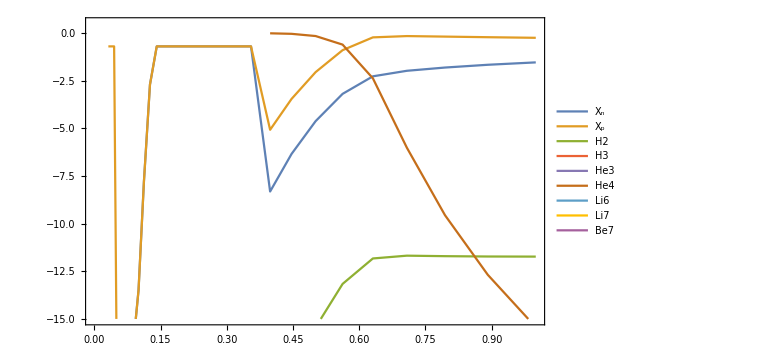

```mathematica
ts=Table[10^i,{i,0,-1.5,-0.05}];
plotdata=TimeSeries[(abundances[#]//Values//Log)&/@ts,{ts}];
ListLinePlot[plotdata,
PlotRange->{-15,0.5},Frame->True,ImageSize->Large,
PlotLegends->Keys[abundances[1]]]
```